```mathematica
Solve[x^3-x^2+x==0, x]
```

{{x→0},{x→(-1)^(1/3)},{x→-(-1)^(2/3)}}

```mathematica
sol2=DSolve[{y'[x]-y[x]==a Sin[x]},y[x],x]
```

{{y[x]→ⅇ^x C[1]-1/2 a (Cos[x]+Sin[x])}}

```mathematica
sol4=DSolve[{y'[x]+y[x]==a Sin[x],y[0]==2},y,x]
```

{{y→Function[{x},-1/2 ⅇ^-x (-4-a+a ⅇ^x Cos[x]-a ⅇ^x Sin[x])]}}

```mathematica
sola1 = sol4/.a->4
```

{{y→Function[{x},-1/2 ⅇ^-x (-4-4+4 ⅇ^x Cos[x]-4 ⅇ^x Sin[x])]}}

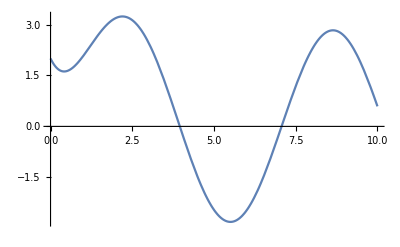

```mathematica
Plot[y[x]/.sola1, {x, 0, 10}]
```

```mathematica
eqn={y'[x]==y[x]^2,y[0]==1};
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},1/(1-x)]}}

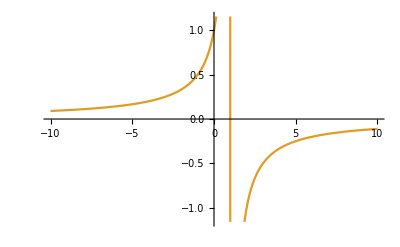

```mathematica
{{y->Function[{x},1/(1-x)]}}
Plot[{x[t]/. sol,y[t]/. sol},{t,-10,10}]
```

```mathematica
Plot[{x[t]/. sol,y[t]/. sol},{t,-10,10}]
```

-Graphics-

```mathematica
eqn=x^2*D[u[x,y],x]+y^2*D[u[x,y],y]-(x+y)*u[x,y];
sol=DSolve[eqn==0,u,{x,y}]
```

```mathematica
eqn=x^2*D[u[x,y],x]+y^2*D[u[x,y],y]-(x+y)*u[x,y];
sol=DSolve[eqn==0,u,{x,y}]
```

{{u→Function[{x,y},x y C[1][1/x-1/y]]}}

```mathematica
fn=u[x,y]/. sol[[1]]/. {C[1][t_]->Sin[t^2]+(t/10)}
```

x y (1/10 (1/x-1/y)+Sin[(1/x-1/y)^2])

```mathematica
Plot3D[fn,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
MaxMemoryUsed[]/1024.^2
```

218.949

## Series

```mathematica
s1 = Series[Log[x+1], {x,0,1}]
s2 = Series[Log[x+1], {x,0,2}]
s3 = Series[Log[x+1], {x,0,3}]
```

x+O[x]^2

x-x^2/2+O[x]^3

x-x^2/2+x^3/3+O[x]^4

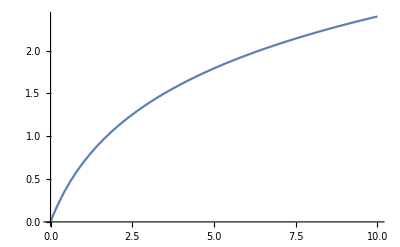

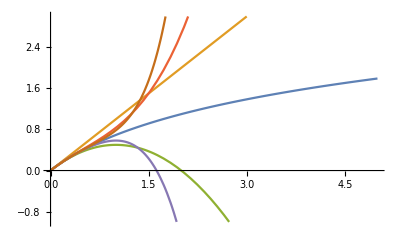

```mathematica
Plot[Log[x+1],{x, 0, 10}]
Plot[{Log[x+1],Evaluate[Table[Normal[Series[Log[1+x], {x,0,n}]],{n,1,5}]]}, {x, 0, 5}, PlotRange->{-1, 3}]
```